# MCMC evaluation Celtic kinship dataset

## Full- and Half-Sibling models

```mathematica
rawD=Import["/Users/stephan_schiffels/dev/celtic_relationship_analysis/model_siblings_output.csv"]//Select[NumberQ[#[[1]]]||StringTake[#[[1]],1]!="#"&]
```

```mathematica
ds=Dataset[AssociationThread[rawD[[1]],#]&/@Rest[rawD]]
```

Dataset[<>]

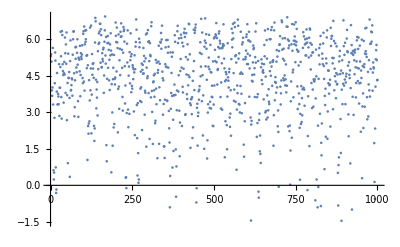

```mathematica
ListPlot[ds[[All,"lp__"]]]
```

Trajectory looks fine, no obvious burn-in or something.

```mathematica
Median[ds[[All,"lp__"]]]
```

4.64648